```mathematica
primeTurn[n_Integer] := Module[{step, rotate, points, i},
  step = {1, 0};
  rotate = {{0, 1}, {-1, 0}};
  points = ConstantArray[0, {n, 2}];
  For[i = 2, i ≤ n, i++,
   points[[i]] = points[[i - 1]] + step;
   If[PrimeQ[i], step = rotate.step]];
  ListLinePlot[points, Axes -> False,
   AspectRatio -> 1, PlotRange -> Full, ImageSize -> Large]]
```

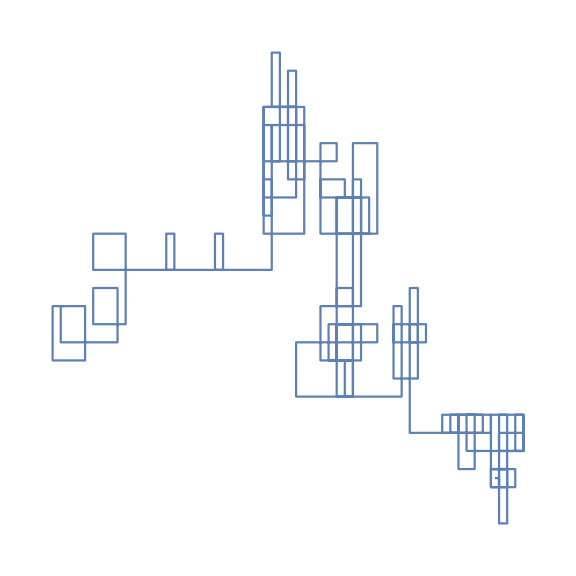

```mathematica
primeTurn[1000]
```